```mathematica
(*----------Basic code to Solve Quantum annealing problems in Mathematica----------*)
```

(*Quantum Annealing in Mathematica:Test the code for n≥3 Qubits, n≥2 Qubits needs some modifications in logic: The code will be used to study various types of feature selections and quantum annealing problems...........*)

```mathematica
σx={{0,1},{1,0}};
```

```mathematica
σy={{0,-I},{I,0}};
```

```mathematica
σz={{1,0},{0,-1}};
```

```mathematica
id2=IdentityMatrix[2];
```

```mathematica
(*code for Initial Hamiltoanin which is prepared in ground state*)
```

```mathematica
Clear[iNitalHamiltonain];
iNitalHamiltonain[n_]:=Module[{l1,l2,d,i2,mYexpression1},
If[n==0||n==1,Print["Provide (n≥2) Qubits"],
l1=Table[1,{i,1,n}];
l2=Table[σ,{i,1,n}];
d=DiagonalMatrix[l1*l2];
i2=d/.{0->id};
mYexpression1=Total[Apply[KroneckerProduct,i2,{1}]];(*Testing: one can check here the correct tensor product expression*)
(-1)*mYexpression1/.{σ->σx,id->id2}]
]
```

```mathematica
iNitalHamiltonain[3]//MatrixForm;
```

(*code for the Magnetific field term ∑_i h_i(σ^z)_i*)

```mathematica
Clear[mAgnetifcField];
mAgnetifcField[n_]:=Module[{i1,l1,l2,mYexpression1,mYexpression2},
SeedRandom[12345];
If[n==0||n==1,Print["Provide (n≥2) Qubits"],
l1=Table[RandomReal[{0,1}],{i,1,n}];
(*List l1 is the list of Magnetic filed strengths*)
l2=Table[σ,{i,1,n}];
i1=DiagonalMatrix[l2]/.{0->id};
mYexpression1=Total[l1*Apply[KroneckerProduct,i1,{1}]];
(*Testing: one can check here the correct tensor product expression*)
mYexpression2=mYexpression1/.{σ->σz,id->id2}]
]
```

```mathematica
mAgnetifcField[3]//MatrixForm;
```

```mathematica
(*code for the Interaction term (∑^n)_(<i,j,i≠j>)Subscript[J, ij] Subscript[σ^z, i] ⊗Subscript[σ^z, j]*)
```

```mathematica
Clear[interaction];
interaction[n_]:=Module[{i,j,l1,l2,l3,eXpression1,eXpression2},
SeedRandom[4567];
l1=Table[id,{i,1,n}];
If[n==0||n==1 ,Print["Provide (n≥2) Qubits"],
If[n==2,Subscript[J, 12]*(KroneckerProduct[σz,id2]+KroneckerProduct[id2,σz]),
(*l2=Table[If[i<j,Subscript[J,i,j],0],{i,1,n},{j,1,n}];*)
(*Basically l2 is an upper-traingular matrix with Cofficients Subscript[J, ij]*)
(*Lets create l2 as a random upper-traingular matrix along with Diagonalwith SeedRandom[12345] fixed: In that sence our Mutual Information matrix is fixed*)
l2=Table[If[i≤j,RandomVariate[NormalDistribution[0,1]],0],{i,1,n},{j,1,n}];
l3=Table[If[i<j,Apply[KroneckerProduct,ReplacePart[l1,{{i},{j}}->σ]],0],{i,1,n},{j,1,n}];
eXpression1=Total[Total[l2*l3]];
(*Testing: one can check here the correct tensor product expression*)
eXpression2=eXpression1/.{σ->σz,id->id2 }]]
]
```

```mathematica
interaction[3]//MatrixForm;
```

```mathematica
Clear[constraint];
constraint[n_]:=Module[{l1,l2,l3,l4,l5,l6,l7},
l1=DiagonalMatrix[Table[σ,{i,1,n}]]/.{0-> id};
l2=Apply[KroneckerProduct,l1,{1}];
l3=Total[l2];(*(∑^n)_i Subscript[σ, i]*)
l4=Table[id,{i,1,n}];
l5=k*Apply[KroneckerProduct,l4];(*k(I⊗I⊗I......)*)
l6=α*(l3-l5)^2;
l7=l6/.{σ->σz,id->id2}
]
```

```mathematica
constraint[3]//MatrixForm;
```

```mathematica
(*code for Problem Hamiltonain Subscript[H^1, p]=Subscript[H, p]+Subscript[αH, constraint]*)
```

```mathematica
Clear[pRoblemHamiltonain];
pRoblemHamiltonain[n_]:=Module[{},
mAgnetifcField[n]+interaction[n]+constraint[n](*With Constraint*)
]
```

```mathematica
pRoblemHamiltonain[3]//MatrixForm;
(*Final Hamiltinan H(s) is the function of paremeters s whcih is used to switch the initial Hamiltonian to problem hamiltonian*)
```

```mathematica
(*Quantum annealing Hamiltonain H(s)*)
```

```mathematica
Clear[qAnnealing];
qAnnealing[n_]:=Module[{},
(1-s)*iNitalHamiltonain[n]+s*pRoblemHamiltonain[n]
]
```

```mathematica
qAnnealing[3]//MatrixForm;
```

```mathematica
(*Now find out the differnce between two initial eiganvalues of the Quantum Annealing Hamiltonain between 0≤s≤1*)
```

```mathematica
Clear[eIgenqAnnealing];
eIgenqAnnealing[n_,k1_]:=Module[{e1,e2,dim,diff},
e1=Table[Table[Min[Eigenvalues[qAnnealing[n]/.{k->k1}]],{s,0,1,0.01}],{α,0,1,0.2}];
dim=Dimensions[e1][[1]];
e2=Table[Table[RankedMin[Eigenvalues[qAnnealing[n]/.{k->k1}],2],{s,0,1,0.01}],{α,0,1,0.2}];
Table[ListLinePlot[{e1[[i]],e2[[i]]},DataRange->{0,1},Frame->True,FrameLabel->{"s","(E_1,E_0)"},PlotLabel->Row@{"α=",N[((i-1)/((dim)-1))]}],{i,1,dim}](*Here we Plot the Ist and 2nd eigenvalues spectrum*)
]
```

```mathematica
(*Results:......for different values of K features and with 0≤α≤1*)
```

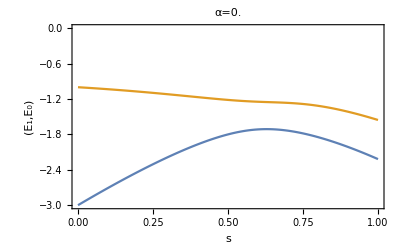
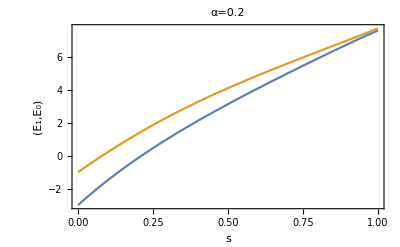
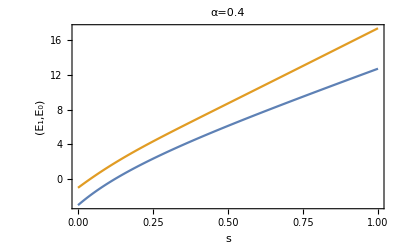
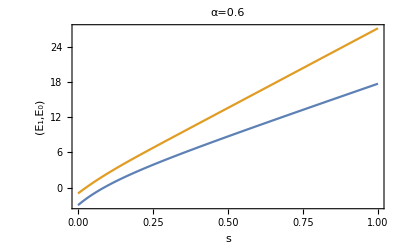
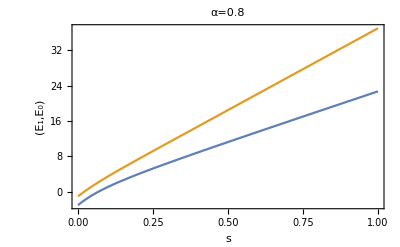
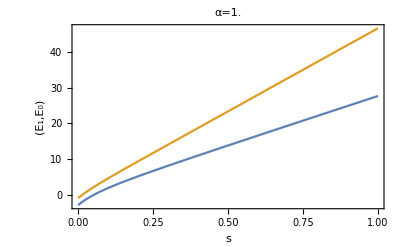

```mathematica
eIgenqAnnealing[3,5]
```

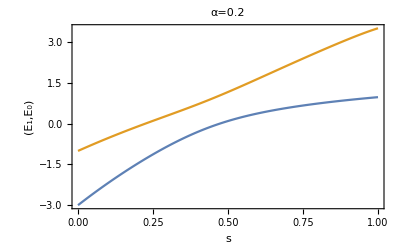
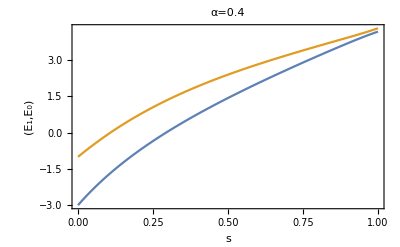
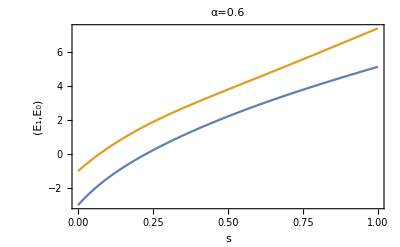
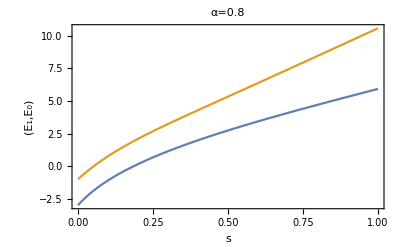
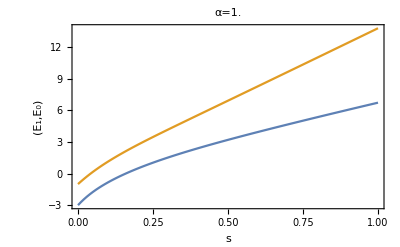
```mathematica
GraphicsGrid[{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}]
```

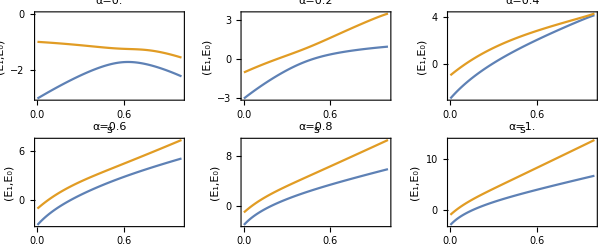

```mathematica
(*Plot Time complexity vs features (k): Time complexity for Global adiabetic quantum computaion approach is given as T=1/(∇E)^2, where ∇E is the energy gap*)
```

```mathematica
Clear[tImeComplexity];
tImeComplexity[n_]:=Module[{e1,e2,dim,diff},
Table[ListLinePlot[Table[(1/(Min[Eigenvalues[qAnnealing[n]]]-RankedMin[Eigenvalues[qAnnealing[n]],2])^2),{k,4,30,0.01}],PlotLabel->Row@{"s=",s|"α=",α},DataRange->{1,30},PlotRange->{0,0.07},PlotStyle->{Red},Frame->True,FrameLabel->{"k","Complexity"}],{s,0.999988,0.999988,0.999988},{α,0.99998,0.99998,0.99998}]
]
```

```mathematica
(*Results:......for different values of K features and with 0≤α≤1*)
```

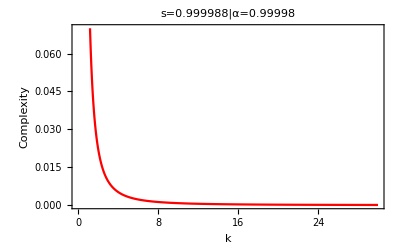

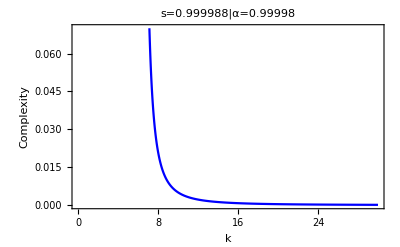

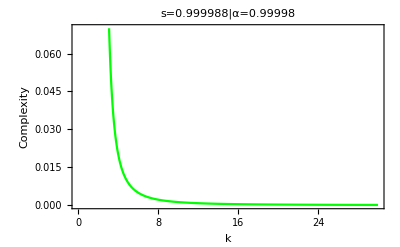

{{-Graphics-}}

```mathematica
tImeComplexity[3]
```

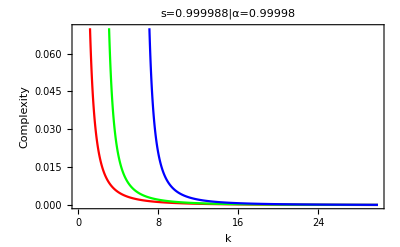

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

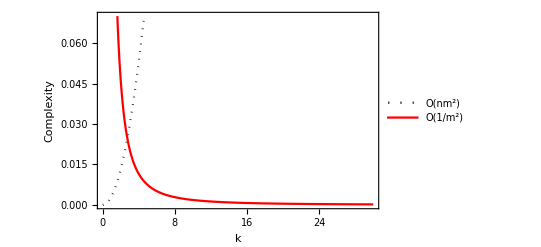

```mathematica
(*Classical and Quantum Complexity plot is below*)
```

```mathematica
GraphicsGrid[{{,}}]
```

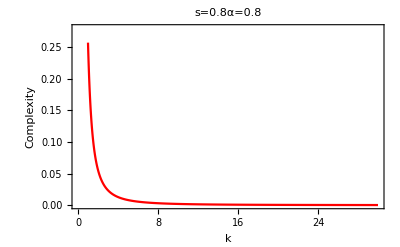
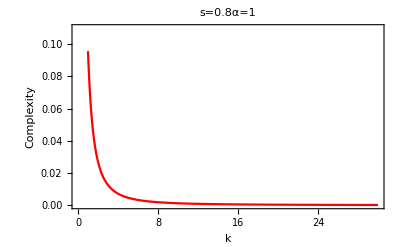
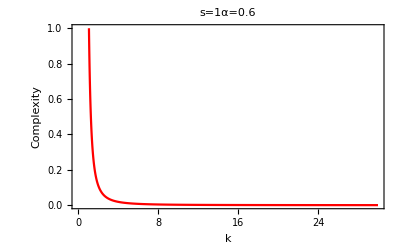
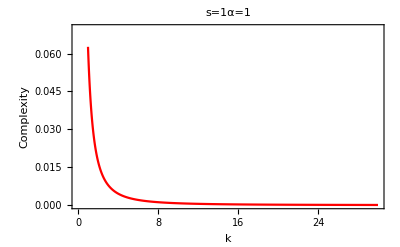
```mathematica
GraphicsGrid[{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}]
```

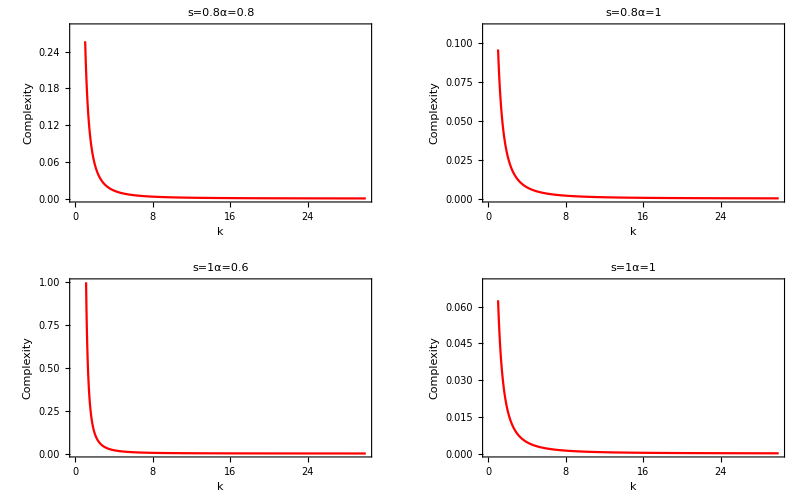

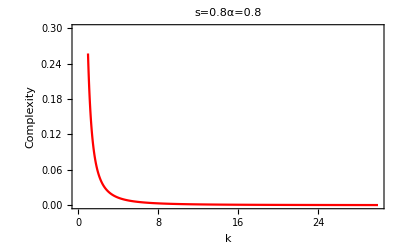

(*We see very Important results in above graphs: As the number of Qubits N is increasing the gap in energy is decreasing and higher is the probability of sucess, this feature is helpful to calculate the complexity as a function of number of qubits*)

(*Now, find out the probability of sucess during the evolution 0≤s≤1*)

(*When Adiabetic theorm is satisfied, we know for s=1, the H(s)=H_(p,) The gound state of H_p encodes the solution and |ψ(s)>≃|ψ_g(0)>, where |ψ_g(0)> is the ground state of H_I*)

(*Let prepare the initial state in equal superposition of N Qubits*)

(*code for Initial state |ψ≥1/(√N)(∑^n)_i|i>=1/(√N)(|00000....>+........|1111...>)*)

(*Write down the corresponding matrix as below*)

```mathematica
Clear[iNitalStatePsi0];
iNitalStatePsi0[n_]:=Module[{l1},
l1=Table[(1/(2^(n/2))),{i,1,2^n}]
]
```

```mathematica
iNitalStatePsi0[3]//MatrixForm;
```

(*Check Normalization of the state*)
Total[(iNitalStatePsi0[3])^2];

(*Now Find out the Time evolution of the state under Quantum annealing Hamiltinain as 
|ψ(t)≥e^-Ht|ψ(0)>*)

(*The time evolution is obtained as |ψ(t)≥e^((-i/ℏ).{H_I.s.(1-s/2)+1/2 H_p.s^2})|ψ(0)>, assume ℏ=1, so we re-write the expression as|ψ(t)=e^(-i.{m})|ψ(0)>, where m=H_I.s.(1-s/2)+1/2 H_p.s^2=(iNitalHamiltonain[n])*s.(1-(s/2))+s^2*(pRoblemHamiltonain[n])) *)

```mathematica
Clear[tImeEvolution];
tImeEvolution[n_,k1_,s1_,α1_]:=Module[{m,l1,dm,m2,psiT,mm,probability,aLphaMatrices,eig,l2,evalues, evectors},
(*m is below calcuclated as, ∫_(s=0)^(s=1) H(s)ⅆs*)
m=(s-(s^2/2))*iNitalHamiltonain[n]+s^2*(pRoblemHamiltonain[n]);
dm=Dimensions[m][[1]];
mm=m/.{k->k1,s->s1,α->α1};
eig=Eigenvalues[mm];
l1={eig,Orthogonalize[Eigenvectors[mm]]};
(*Now diagonalise m and calculate e^-iHt.........*)m2=Sum[Exp[(-I)*l1[[1]][[i]]]*(ConjugateTranspose[{l1[[2]][[i]]}].{l1[[2]][[i]]}),{i,1,dm}];
(*Apply unitary matrix e^-im to the initial state and calculate time evolution*)
          psiT=m2.iNitalStatePsi0[n];
(*Here calculate the ground state of Subscript[H, p]*)
{evalues, evectors}=Eigensystem[pRoblemHamiltonain[n]/.{k->k1,α-> α1}];
  SortBy[#,Abs[#[1]]]& @Transpose[{evalues, evectors}];
            l2=First @ SortBy[#, Abs[#[1]]] & @Transpose[{evalues, evectors}];
   (*Ground state of Subscript[H, p] with lowest eigenvalue*)
    l2[[2]];
(*Calculate the probbaility of sucess*)
   probability=Abs[(((l2[[2]]).psiT)*Conjugate[(l2[[2]]).psiT])]
]
```

```mathematica
Clear[probKN];
 probKN[n_]:=Module[{},
Table[ListLinePlot[Table[Re[tImeEvolution[n,k,s,α]],{k,1,30,0.01}],PlotLabel->Row@{"s=",s|"α=",α},PlotStyle->{Red},PlotRange->{0,0.5},DataRange->{1,30},Frame->True,FrameLabel->{"k","Prob."}],{s,0,1,0.2},{α,0,1,0.2}]
]
```

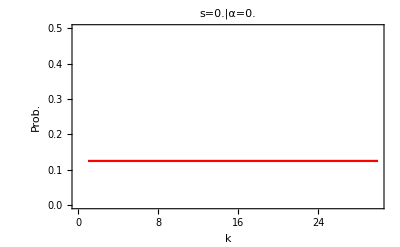
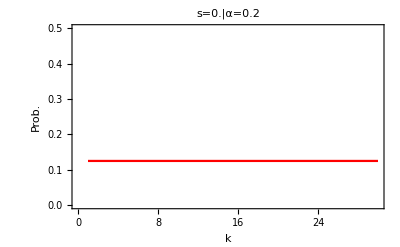
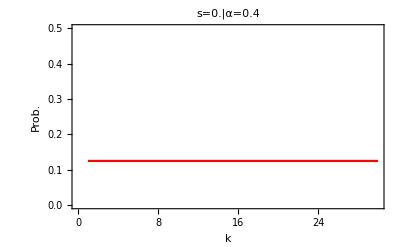
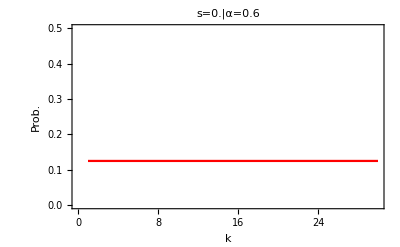
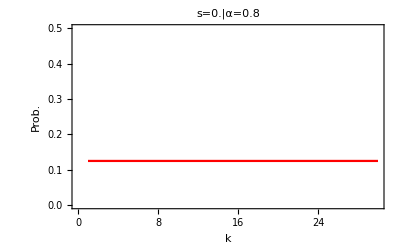
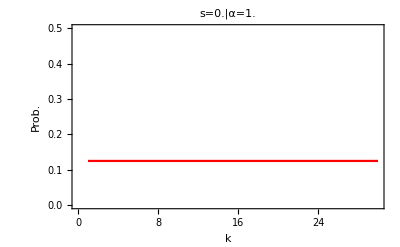
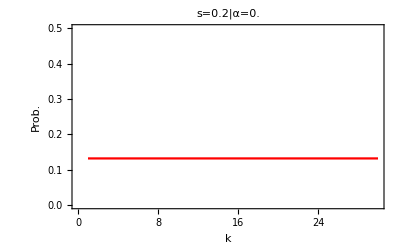
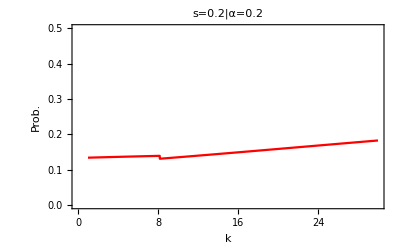

```mathematica
probKN[3]
```

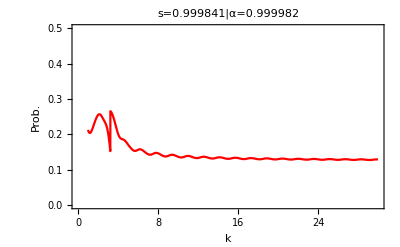
```mathematica
GraphicsGrid[{{-Graphics-,-Graphics-,-Graphics-}}]
```

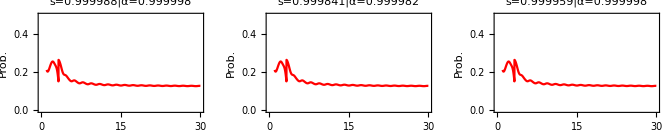

```mathematica
(*What is the effect of the ratio of (n/k) on Probability of sucess*)
```

```mathematica
Clear[hist];
hist[n_]:=Module[{},
Table[{
Histogram[Table[Re[tImeEvolution[n,k,s,α]],{k,1,15,0.01}],15,"Probability",PlotLabel->Row@{"s=",s|"α=",α} ,ChartElementFunction->"GlassRectangle",ChartStyle->{Red},PlotRangePadding->Scaled[.12],PlotTheme->"Detailed"]},{α,0.999998,0.999998,0.999998},{s,0.999959,0.999959,0.999959}]
]
```

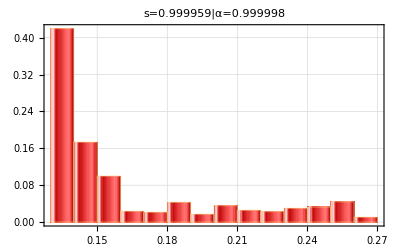

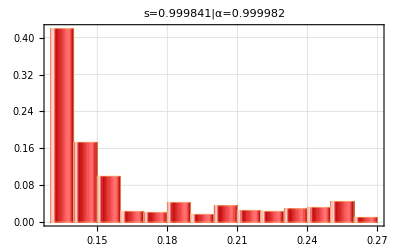

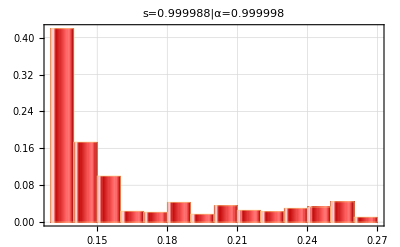

```mathematica
hist[3]
```

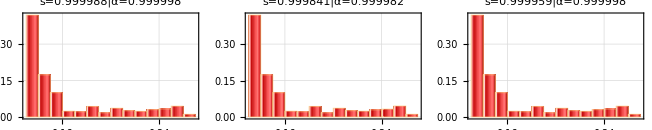

```mathematica
GraphicsGrid[{{-Graphics-,-Graphics-,-Graphics-}}]
```

```mathematica
Quit
```